# CNKI -Graphics-

## Clear memory

```mathematica
ClearAll[xml]
```

```mathematica
ClearAll[authors]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
MemoryInUse[$FrontEnd]
```

55302672

```mathematica
MaxMemoryUsed[]
```

11927392

```mathematica
MemoryConstrained[Cases[xml,XMLElement["authors",_,authors_]->authors,Infinity],1]
```

$Aborted

## Import data

### Import xml

```mathematica
xml=Import["D:/micro-blog/citation network analysis/gjxwj11.xml"];
```

```mathematica
authors=Cases[xml,XMLElement["authors",_,authors_]->authors,Infinity]
```

{{XMLElement[author,{},{XMLElement[style,{face→normal,font→default,size→100%},{庄廷江,}]}]},{XMLElement[author,{},{XMLElement[style,{face→normal,font→default,size→100%},{朱至刚,}]}]},{XMLElement[author,{},{XMLElement[style,{face→normal,font→default,size→100%},{朱东芹,}]}]},«354»,{XMLElement[author,{},{XMLElement[style,{face→normal,font→default,size→100%},{《中国媒介传播"维德守法"状况及评价报告》课题组,}]}]},{XMLElement[author,{},{XMLElement[style,{face→normal,font→default,size→100%},{《中国传媒发展指数报告》项目组,}]}]}}

```mathematica
(*This results in blanks which is very weird.)
```

```mathematica
(*authors=Cases[xml,XMLElement["author",_,{XMLElement["style",_,authors_]}]->authors,Infinity])
```

```mathematica
names=Flatten@Cases[#,XMLElement["author",_,{XMLElement["style",_,names_]}]->names]&/@authors;
```

```mathematica
Length[names]
```

359

```mathematica
names
```

{{庄廷江,},{朱至刚,},{朱东芹,},{周勇,,郑敏,},{周勇,},{周勇,},{周叶飞,},{周小普,,王冲,},{周翔,},{周蔚华,,闫伟华,},{周俊,},{周俊,},{周军,},{周卷施,},{周卷施,},{周丹,},{周葆华,},{钟智锦,},{钟新,,孙晔,},{钟新,,何娟,},{钟新,,韩寒,},{中国受众媒介‘接触, 使用’状态定量研究 课题组},{郑从金,},{郑保卫,},{赵云泽,,付冰清,},{赵云泽,},{赵永华,},{赵心树,},{赵文晶,,陈秀玮,},{赵双阁,,艾岚,},{赵靳秋,,郝晓鸣,},{赵晋,,李彪,,章含泽,,张盖伦,},{赵晋,},{赵鸿燕,,李金慧,},{张子旭,},{张志,},{张征,,张玉荣,},{张毓强,},{张妤玟,},{张咏华,,戴长征,},{张艳秋,},{张歆,,郑笑眉,,张琛,},{张晓辉,},{张文祥,},{张威,},{张涛甫,},{张少元,,蒋晓丽,},{张蕾,},{张雷,,王勇,},{张巨岩,,巩昕崸,,宋婧,},{张晋升,,谢璇,},{张劲松,,廖维晓,},{张健,,佘贻明,},{张健,},{张建中,,任孟山,},{张辉锋,},{张鸿霞,},{张放,},{张斌,},{张佰明,},{云国强,,吴靖,},{袁军,},{袁靖华,},{喻国明,,张佰明,,胥琳佳,,吴文汐,},{喻国明,,王斌,},{喻国明,,李彪,,丁汉青,,王菲,,胥琳佳,},{禹卫华,},{于丹,,张洪忠,,杨东菊,},{尹瑛,},{尹兴,},{尹明华,},{尹连根,},{尹鸿,},{殷俊,,孟育耀,},{易文,},{易前良,,王朝红,},{叶青青,},{叶青青,},{叶冲,,庞荣棣,},{姚晓鸥,},{杨颖,},{杨银娟,},{杨银娟,},{杨凯,},{杨保军,},{杨保军,},{阳美燕,},{阳海洪,},{闫岩,},{薛可,,陈晞,,余明阳,},{许子豪,},{许子豪,},{徐明,},{徐明,},{徐明,},{徐泓,},{徐帆,},{谢进川,},{肖叶飞,},{肖燕雄,,熊敏,},{肖伟,},{夏冠英,},{吴廷俊,},{吴麟,},{吴来安,},{吴来安,},{吴静,},{吴靖,},{吴璟薇,},{吴辉,},{吴昊,},{吴果中,,尹志伟,},{吴飞,,丁志远,},{吴飞,,丁志远,},{翁昌寿,,李建霞,,方莉,},{翁昌寿,},{魏海岩,},{王正祥,},{王勇,},{王亦高,},{王祎,},{王秀丽,,韩纲,},{王晓兰,},{王伟亮,},{王润泽,},{王润泽,},{王朋进,},{王军元,,王静,},{王海,},{王樊逸,},{王翠荣,,吴廷俊,},{王辰瑶,},{王朝阳,},{王斌,},{汪露,},{万小广,},{涂晓华,},{涂鸣华,},{涂凌波,},{涂光晋,,宫贺,},{田边,},{唐海江,,唐雨晴,},{唐海江,},{谭云明,,袁援,},{谭宇菲,},{谭天,},{孙晔,},{孙燕清,,高敬,},{孙旭培,,卢家银,},{孙旭培,,董柳,},{孙玮,},{孙庚,},{孙彩芹,},{隋岩,},{宋小卫,},{司马兰,},{史志高,},{石玮,},{师曾志,},{师曾志,},{邵华冬,,杜国清,},{邱鸿峰,},{乔治·索瓦凯斯,,科斯塔·阿高什,,阿西娜·佐托斯,,安德烈·威格利斯,,赵彦华,},{齐辉,,王翠荣,},{齐辉,},{彭兰,},{彭兰,},{裴峥,},{潘文年,},{潘霁,},{牛静,},{倪宁,,张勤,},{倪宁,},{尼古拉斯·卡尔,,钟新,,陆佳怡,},{孟伟,},{孟鹏,},{毛章清,},{麦尚文,},{马少华,,刘铮,},{马克·迪耶兹,,周俊,,李玉洁,},{吕鹏,},{吕鹏,},{罗雪蕾,},{罗慧,},{罗锋,},{罗斌,,宋素红,},{罗彬,},{路鹏程,},{陆亨,},{陆斌,},{刘自雄,,许雯,,高亚男,},{刘勇,},{刘寅斌,,肖萍,,陈永,},{刘耀辉,,张璇,},{刘扬,},{刘泱育,},{刘泱育,},{刘艳凤,},{刘学义,},{刘小燕,},{刘涛,},{刘涛,},{刘舜发,,钱践,},{刘蒙之,},{刘立华,},{刘开骅,},{刘兢,},{刘津,},{刘洁,},{刘继忠,},{刘海龙,},{刘东倩,},{刘琛,},{林玉凤,},{林爱珺,,孙姣姣,},{廖秉宜,},{李瞻,},{李瞻,},{李玉洁,},{李玉洁,},{李异平,},{李彦冰,,荆学民,},{李欣人,},{李霞,},{李习文,},{李武,},{李卫华,},{李统兴,},{李松蕾,},{李松蕾,},{李松蕾,},{李青藜,},{李明伟,},{李名亮,},{李漫,},{李理,},{李开军,},{李杰琼,},{李杰琼,},{李杰琼,},{李杰琼,},{李杰琼,},{李宏杨,},{李宏杨,},{李宏杨,},{李宏杨,},{李宏杨,},{李红涛,,黄顺铭,},{李寒松,},{李贵升,},{李道芳,},{李丹林,},{李承华,},{李彬,,刘宪阁,},{雷蔚真,,何睿,},{雷蔚真,,曹小杰,},{雷霏,},{匡文波,,高岩,},{康瑾,},{蒋忠波,,邓若伊,},{江凌,},{贾文山,,岳媛,},{贾乐蓉,},{贾广惠,},{黄晓军,},{黄瑞刚,},{黄华,},{黄河,,江凡,},{黄河,},{黄旦,,瞿轶羿,},{黄春平,},{胡正强,},{胡翼青,},{胡春阳,},{胡百精,},{贺碧霄,},{何舟,,陈先红,},{韩素梅,},{郭晓科,},{郭光华,},{关琮严,},{谷长岭,,叶凤美,},{谷长岭,},{谷长岭,},{谷虹,},{高一飞,},{高金萍,,罗智勇,},{高海波,},{高海波,},{高贵武,,邓燕玲,},{高钢,},{高钢,},{甘险峰,},{付玉辉,},{付玉辉,},{菲利普·赛博,,陆佳怡,,钟新,},{方师师,,於红梅,},{方洁,},{方建移,},{方建移,},{樊亚平,},{董媛媛,,王涪宁,},{董天策,,胡丹,},{董天策,,蔡慧,},{董乐铄,,庞云黠,},{丁和根,,林吟昕,},{丁汉青,,李亚菲,},{邓绍根,},{戴元光,,夏寅,},{崔远航,},{初广志,},{程忠良,},{陈卓,},{陈致中,},{陈志强,},{陈韵博,},{陈玉,},{陈阳,},{陈绚,},{陈卫星,,徐桂权,},{陈天助,},{陈韬文,,李立峯,},{陈堂发,},{陈世华,},{陈世华,},{陈霖,,邢强,},{陈立新,},{陈力丹,,王晶,},{陈力丹,},{陈力丹,},{陈力丹,},{陈凯茵,},{陈俊妮,,陈俊峰,},{陈俊妮,},{陈静静,},{陈健强,,刘师健,},{陈建群,},{陈建群,},{陈继静,},{陈辉,},{陈刚,},{常江,},{曾一果,},{曾一果,},{曾晓剑,},{曾庆香,,郭磊,},{蔡琰,,臧国仁,},{蔡雯,,莫妤,},{蔡雯,},{蔡斐,},{比畅,},{本刊编辑部,},{本刊编辑部,},{本刊编辑部,},{白净,},{艾红红,,朱丽丽,},{《中国媒介传播"维德守法"状况及评价报告》课题组,,陈绚,},{《中国媒介传播"维德守法"状况及评价报告》课题组,},{《中国传媒发展指数报告》项目组,}}

### Caculate the distribution

```mathematica
table=Sort[Tally[Length[#]&/@names],#1[[1]]<#2[[1]]&]
```

{{1,267},{2,78},{3,10},{4,2},{5,2}}

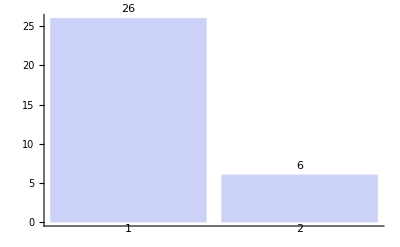

```mathematica
BarChart[{26,6},LabelingFunction->(Placed[#,Above]&),ChartLabels->{Placed[{"Group 1","Group 2"},Center,rotateLabel],{"1","2"}}]
```

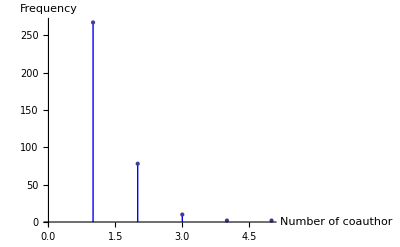

```mathematica
ListPlot[table,Filling->Axis,FillingStyle->Blue,AxesLabel->{"Number of coauthor","Frequency"},AxesOrigin->{0,0}]
```

## Author Participation

### Split the coauthors

```mathematica
split=SplitBy[#,",,"]&/@Sort[names]
```

{{{倪宁,}},{{刘兢,}},{{刘勇,}},{{刘扬,}},{{刘洁,}},{{刘津,}},{{刘涛,}},{{刘涛,}},{{刘琛,}},{{吕鹏,}},{{吕鹏,}},{{吴昊,}},{{吴辉,}},{{吴靖,}},{{吴静,}},{{吴麟,}},{{周丹,}},{{周俊,}},{{周俊,}},{{周军,}},{{周勇,}},{{周勇,}},{{周翔,}},{{孙庚,}},{{孙晔,}},{{孙玮,}},{{孟伟,}},{{孟鹏,}},{{尹兴,}},{{尹瑛,}},{{尹鸿,}},{{常江,}},{{康瑾,}},{{张健,}},{{张威,}},{{张志,}},{{张放,}},{{张斌,}},{{张蕾,}},{{彭兰,}},{{彭兰,}},{{徐帆,}},{{徐明,}},{{徐明,}},{{徐明,}},{{徐泓,}},{{方洁,}},{{易文,}},{{李武,}},{{李漫,}},{{李理,}},{{李瞻,}},{{李瞻,}},{{李霞,}},{{杨凯,}},{{杨颖,}},{{比畅,}},{{江凌,}},{{汪露,}},{{潘霁,}},{{牛静,}},{{王勇,}},{{王斌,}},{{王海,}},{{王祎,}},{{田边,}},{{白净,}},{{石玮,}},{{罗彬,}},{{罗慧,}},{{罗锋,}},{{肖伟,}},{{蔡斐,}},{{蔡雯,}},{{袁军,}},{{裴峥,}},{{谭天,}},{{谷虹,}},{{赵晋,}},{{闫岩,}},{{陆亨,}},{{陆斌,}},{{陈刚,}},{{陈卓,}},{{陈玉,}},{{陈绚,}},{{陈辉,}},{{陈阳,}},{{隋岩,}},{{雷霏,}},{{高钢,}},{{高钢,}},{{黄华,}},{{黄河,}},{{齐辉,}},{{万小广,}},{{付玉辉,}},{{付玉辉,}},{{关琮严,}},{{刘东倩,}},{{刘学义,}},{{刘小燕,}},{{刘开骅,}},{{刘泱育,}},{{刘泱育,}},{{刘海龙,}},{{刘立华,}},{{刘继忠,}},{{刘艳凤,}},{{刘蒙之,}},{{初广志,}},{{史志高,}},{{叶青青,}},{{叶青青,}},{{司马兰,}},{{吴廷俊,}},{{吴来安,}},{{吴来安,}},{{吴璟薇,}},{{周卷施,}},{{周卷施,}},{{周叶飞,}},{{周葆华,}},{{唐海江,}},{{夏冠英,}},{{姚晓鸥,}},{{孙彩芹,}},{{宋小卫,}},{{尹明华,}},{{尹连根,}},{{崔远航,}},{{师曾志,}},{{师曾志,}},{{庄廷江,}},{{廖秉宜,}},{{张佰明,}},{{张妤玟,}},{{张子旭,}},{{张文祥,}},{{张晓辉,}},{{张毓强,}},{{张涛甫,}},{{张艳秋,}},{{张辉锋,}},{{张鸿霞,}},{{方建移,}},{{方建移,}},{{曾一果,}},{{曾一果,}},{{曾晓剑,}},{{朱东芹,}},{{朱至刚,}},{{李丹林,}},{{李习文,}},{{李卫华,}},{{李名亮,}},{{李宏杨,}},{{李宏杨,}},{{李宏杨,}},{{李宏杨,}},{{李宏杨,}},{{李寒松,}},{{李开军,}},{{李异平,}},{{李承华,}},{{李明伟,}},{{李杰琼,}},{{李杰琼,}},{{李杰琼,}},{{李杰琼,}},{{李杰琼,}},{{李松蕾,}},{{李松蕾,}},{{李松蕾,}},{{李欣人,}},{{李玉洁,}},{{李玉洁,}},{{李统兴,}},{{李贵升,}},{{李道芳,}},{{李青藜,}},{{杨保军,}},{{杨保军,}},{{杨银娟,}},{{杨银娟,}},{{林玉凤,}},{{樊亚平,}},{{毛章清,}},{{涂凌波,}},{{涂晓华,}},{{涂鸣华,}},{{潘文年,}},{{王亦高,}},{{王伟亮,}},{{王晓兰,}},{{王朋进,}},{{王朝阳,}},{{王樊逸,}},{{王正祥,}},{{王润泽,}},{{王润泽,}},{{王辰瑶,}},{{甘险峰,}},{{禹卫华,}},{{程忠良,}},{{罗雪蕾,}},{{翁昌寿,}},{{肖叶飞,}},{{胡春阳,}},{{胡正强,}},{{胡百精,}},{{胡翼青,}},{{袁靖华,}},{{许子豪,}},{{许子豪,}},{{谢进川,}},{{谭宇菲,}},{{谷长岭,}},{{谷长岭,}},{{贺碧霄,}},{{贾乐蓉,}},{{贾广惠,}},{{赵云泽,}},{{赵心树,}},{{赵永华,}},{{路鹏程,}},{{邓绍根,}},{{邱鸿峰,}},{{郑从金,}},{{郑保卫,}},{{郭光华,}},{{郭晓科,}},{{钟智锦,}},{{阳海洪,}},{{阳美燕,}},{{陈世华,}},{{陈世华,}},{{陈俊妮,}},{{陈凯茵,}},{{陈力丹,}},{{陈力丹,}},{{陈力丹,}},{{陈堂发,}},{{陈天助,}},{{陈建群,}},{{陈建群,}},{{陈志强,}},{{陈立新,}},{{陈继静,}},{{陈致中,}},{{陈静静,}},{{陈韵博,}},{{韩素梅,}},{{高一飞,}},{{高海波,}},{{高海波,}},{{魏海岩,}},{{麦尚文,}},{{黄春平,}},{{黄晓军,}},{{黄瑞刚,}},{{本刊编辑部,}},{{本刊编辑部,}},{{本刊编辑部,}},{{《中国传媒发展指数报告》项目组,}},{{《中国媒介传播"维德守法"状况及评价报告》课题组,}},{{中国受众媒介‘接触, 使用’状态定量研究 课题组}},{{何舟,},{陈先红,}},{{倪宁,},{张勤,}},{{叶冲,},{庞荣棣,}},{{吴飞,},{丁志远,}},{{吴飞,},{丁志远,}},{{周勇,},{郑敏,}},{{张健,},{佘贻明,}},{{张征,},{张玉荣,}},{{张雷,},{王勇,}},{{李彬,},{刘宪阁,}},{{殷俊,},{孟育耀,}},{{罗斌,},{宋素红,}},{{蔡琰,},{臧国仁,}},{{蔡雯,},{莫妤,}},{{钟新,},{何娟,}},{{钟新,},{孙晔,}},{{钟新,},{韩寒,}},{{陈霖,},{邢强,}},{{黄旦,},{瞿轶羿,}},{{黄河,},{江凡,}},{{齐辉,},{王翠荣,}},{{丁和根,},{林吟昕,}},{{丁汉青,},{李亚菲,}},{{云国强,},{吴靖,}},{{刘耀辉,},{张璇,}},{{刘舜发,},{钱践,}},{{匡文波,},{高岩,}},{{吴果中,},{尹志伟,}},{{周小普,},{王冲,}},{{周蔚华,},{闫伟华,}},{{唐海江,},{唐雨晴,}},{{喻国明,},{王斌,}},{{孙旭培,},{董柳,}},{{孙旭培,},{卢家银,}},{{孙燕清,},{高敬,}},{{张劲松,},{廖维晓,}},{{张咏华,},{戴长征,}},{{张少元,},{蒋晓丽,}},{{张建中,},{任孟山,}},{{张晋升,},{谢璇,}},{{戴元光,},{夏寅,}},{{方师师,},{於红梅,}},{{易前良,},{王朝红,}},{{曾庆香,},{郭磊,}},{{李彦冰,},{荆学民,}},{{李红涛,},{黄顺铭,}},{{林爱珺,},{孙姣姣,}},{{涂光晋,},{宫贺,}},{{王军元,},{王静,}},{{王秀丽,},{韩纲,}},{{王翠荣,},{吴廷俊,}},{{肖燕雄,},{熊敏,}},{{艾红红,},{朱丽丽,}},{{董乐铄,},{庞云黠,}},{{董天策,},{胡丹,}},{{董天策,},{蔡慧,}},{{董媛媛,},{王涪宁,}},{{蒋忠波,},{邓若伊,}},{{谭云明,},{袁援,}},{{谷长岭,},{叶凤美,}},{{贾文山,},{岳媛,}},{{赵云泽,},{付冰清,}},{{赵双阁,},{艾岚,}},{{赵文晶,},{陈秀玮,}},{{赵靳秋,},{郝晓鸣,}},{{赵鸿燕,},{李金慧,}},{{邵华冬,},{杜国清,}},{{陈俊妮,},{陈俊峰,}},{{陈健强,},{刘师健,}},{{陈力丹,},{王晶,}},{{陈卫星,},{徐桂权,}},{{陈韬文,},{李立峯,}},{{雷蔚真,},{何睿,}},{{雷蔚真,},{曹小杰,}},{{马少华,},{刘铮,}},{{高贵武,},{邓燕玲,}},{{高金萍,},{罗智勇,}},{{《中国媒介传播"维德守法"状况及评价报告》课题组,},{陈绚,}},{{于丹,},{张洪忠,},{杨东菊,}},{{张歆,},{郑笑眉,},{张琛,}},{{薛可,},{陈晞,},{余明阳,}},{{刘寅斌,},{肖萍,},{陈永,}},{{刘自雄,},{许雯,},{高亚男,}},{{张巨岩,},{巩昕崸,},{宋婧,}},{{翁昌寿,},{李建霞,},{方莉,}},{{尼古拉斯·卡尔,},{钟新,},{陆佳怡,}},{{菲利普·赛博,},{陆佳怡,},{钟新,}},{{马克·迪耶兹,},{周俊,},{李玉洁,}},{{赵晋,},{李彪,},{章含泽,},{张盖伦,}},{{喻国明,},{张佰明,},{胥琳佳,},{吴文汐,}},{{喻国明,},{李彪,},{丁汉青,},{王菲,},{胥琳佳,}},{{乔治·索瓦凯斯,},{科斯塔·阿高什,},{阿西娜·佐托斯,},{安德烈·威格利斯,},{赵彦华,}}}

### Permutations of co-author

```mathematica
data=Permutations[#,{3}]&/@split;
```

### Select single author

```mathematica
single=Select[#,Length[#]<=1&]&/@split
```

{{{倪宁,}},{{刘兢,}},{{刘勇,}},{{刘扬,}},{{刘洁,}},{{刘津,}},{{刘涛,}},{{刘涛,}},{{刘琛,}},{{吕鹏,}},{{吕鹏,}},{{吴昊,}},{{吴辉,}},{{吴靖,}},{{吴静,}},{{吴麟,}},{{周丹,}},{{周俊,}},{{周俊,}},{{周军,}},{{周勇,}},{{周勇,}},{{周翔,}},{{孙庚,}},{{孙晔,}},{{孙玮,}},{{孟伟,}},{{孟鹏,}},{{尹兴,}},{{尹瑛,}},{{尹鸿,}},{{常江,}},{{康瑾,}},{{张健,}},{{张威,}},{{张志,}},{{张放,}},{{张斌,}},{{张蕾,}},{{彭兰,}},{{彭兰,}},{{徐帆,}},{{徐明,}},{{徐明,}},{{徐明,}},{{徐泓,}},{{方洁,}},{{易文,}},{{李武,}},{{李漫,}},{{李理,}},{{李瞻,}},{{李瞻,}},{{李霞,}},{{杨凯,}},{{杨颖,}},{{比畅,}},{{江凌,}},{{汪露,}},{{潘霁,}},{{牛静,}},{{王勇,}},{{王斌,}},{{王海,}},{{王祎,}},{{田边,}},{{白净,}},{{石玮,}},{{罗彬,}},{{罗慧,}},{{罗锋,}},{{肖伟,}},{{蔡斐,}},{{蔡雯,}},{{袁军,}},{{裴峥,}},{{谭天,}},{{谷虹,}},{{赵晋,}},{{闫岩,}},{{陆亨,}},{{陆斌,}},{{陈刚,}},{{陈卓,}},{{陈玉,}},{{陈绚,}},{{陈辉,}},{{陈阳,}},{{隋岩,}},{{雷霏,}},{{高钢,}},{{高钢,}},{{黄华,}},{{黄河,}},{{齐辉,}},{{万小广,}},{{付玉辉,}},{{付玉辉,}},{{关琮严,}},{{刘东倩,}},{{刘学义,}},{{刘小燕,}},{{刘开骅,}},{{刘泱育,}},{{刘泱育,}},{{刘海龙,}},{{刘立华,}},{{刘继忠,}},{{刘艳凤,}},{{刘蒙之,}},{{初广志,}},{{史志高,}},{{叶青青,}},{{叶青青,}},{{司马兰,}},{{吴廷俊,}},{{吴来安,}},{{吴来安,}},{{吴璟薇,}},{{周卷施,}},{{周卷施,}},{{周叶飞,}},{{周葆华,}},{{唐海江,}},{{夏冠英,}},{{姚晓鸥,}},{{孙彩芹,}},{{宋小卫,}},{{尹明华,}},{{尹连根,}},{{崔远航,}},{{师曾志,}},{{师曾志,}},{{庄廷江,}},{{廖秉宜,}},{{张佰明,}},{{张妤玟,}},{{张子旭,}},{{张文祥,}},{{张晓辉,}},{{张毓强,}},{{张涛甫,}},{{张艳秋,}},{{张辉锋,}},{{张鸿霞,}},{{方建移,}},{{方建移,}},{{曾一果,}},{{曾一果,}},{{曾晓剑,}},{{朱东芹,}},{{朱至刚,}},{{李丹林,}},{{李习文,}},{{李卫华,}},{{李名亮,}},{{李宏杨,}},{{李宏杨,}},{{李宏杨,}},{{李宏杨,}},{{李宏杨,}},{{李寒松,}},{{李开军,}},{{李异平,}},{{李承华,}},{{李明伟,}},{{李杰琼,}},{{李杰琼,}},{{李杰琼,}},{{李杰琼,}},{{李杰琼,}},{{李松蕾,}},{{李松蕾,}},{{李松蕾,}},{{李欣人,}},{{李玉洁,}},{{李玉洁,}},{{李统兴,}},{{李贵升,}},{{李道芳,}},{{李青藜,}},{{杨保军,}},{{杨保军,}},{{杨银娟,}},{{杨银娟,}},{{林玉凤,}},{{樊亚平,}},{{毛章清,}},{{涂凌波,}},{{涂晓华,}},{{涂鸣华,}},{{潘文年,}},{{王亦高,}},{{王伟亮,}},{{王晓兰,}},{{王朋进,}},{{王朝阳,}},{{王樊逸,}},{{王正祥,}},{{王润泽,}},{{王润泽,}},{{王辰瑶,}},{{甘险峰,}},{{禹卫华,}},{{程忠良,}},{{罗雪蕾,}},{{翁昌寿,}},{{肖叶飞,}},{{胡春阳,}},{{胡正强,}},{{胡百精,}},{{胡翼青,}},{{袁靖华,}},{{许子豪,}},{{许子豪,}},{{谢进川,}},{{谭宇菲,}},{{谷长岭,}},{{谷长岭,}},{{贺碧霄,}},{{贾乐蓉,}},{{贾广惠,}},{{赵云泽,}},{{赵心树,}},{{赵永华,}},{{路鹏程,}},{{邓绍根,}},{{邱鸿峰,}},{{郑从金,}},{{郑保卫,}},{{郭光华,}},{{郭晓科,}},{{钟智锦,}},{{阳海洪,}},{{阳美燕,}},{{陈世华,}},{{陈世华,}},{{陈俊妮,}},{{陈凯茵,}},{{陈力丹,}},{{陈力丹,}},{{陈力丹,}},{{陈堂发,}},{{陈天助,}},{{陈建群,}},{{陈建群,}},{{陈志强,}},{{陈立新,}},{{陈继静,}},{{陈致中,}},{{陈静静,}},{{陈韵博,}},{{韩素梅,}},{{高一飞,}},{{高海波,}},{{高海波,}},{{魏海岩,}},{{麦尚文,}},{{黄春平,}},{{黄晓军,}},{{黄瑞刚,}},{{本刊编辑部,}},{{本刊编辑部,}},{{本刊编辑部,}},{{《中国传媒发展指数报告》项目组,}},{{《中国媒介传播"维德守法"状况及评价报告》课题组,}},{{中国受众媒介‘接触, 使用’状态定量研究 课题组}},{{何舟,},{陈先红,}},{{倪宁,},{张勤,}},{{叶冲,},{庞荣棣,}},{{吴飞,},{丁志远,}},{{吴飞,},{丁志远,}},{{周勇,},{郑敏,}},{{张健,},{佘贻明,}},{{张征,},{张玉荣,}},{{张雷,},{王勇,}},{{李彬,},{刘宪阁,}},{{殷俊,},{孟育耀,}},{{罗斌,},{宋素红,}},{{蔡琰,},{臧国仁,}},{{蔡雯,},{莫妤,}},{{钟新,},{何娟,}},{{钟新,},{孙晔,}},{{钟新,},{韩寒,}},{{陈霖,},{邢强,}},{{黄旦,},{瞿轶羿,}},{{黄河,},{江凡,}},{{齐辉,},{王翠荣,}},{{丁和根,},{林吟昕,}},{{丁汉青,},{李亚菲,}},{{云国强,},{吴靖,}},{{刘耀辉,},{张璇,}},{{刘舜发,},{钱践,}},{{匡文波,},{高岩,}},{{吴果中,},{尹志伟,}},{{周小普,},{王冲,}},{{周蔚华,},{闫伟华,}},{{唐海江,},{唐雨晴,}},{{喻国明,},{王斌,}},{{孙旭培,},{董柳,}},{{孙旭培,},{卢家银,}},{{孙燕清,},{高敬,}},{{张劲松,},{廖维晓,}},{{张咏华,},{戴长征,}},{{张少元,},{蒋晓丽,}},{{张建中,},{任孟山,}},{{张晋升,},{谢璇,}},{{戴元光,},{夏寅,}},{{方师师,},{於红梅,}},{{易前良,},{王朝红,}},{{曾庆香,},{郭磊,}},{{李彦冰,},{荆学民,}},{{李红涛,},{黄顺铭,}},{{林爱珺,},{孙姣姣,}},{{涂光晋,},{宫贺,}},{{王军元,},{王静,}},{{王秀丽,},{韩纲,}},{{王翠荣,},{吴廷俊,}},{{肖燕雄,},{熊敏,}},{{艾红红,},{朱丽丽,}},{{董乐铄,},{庞云黠,}},{{董天策,},{胡丹,}},{{董天策,},{蔡慧,}},{{董媛媛,},{王涪宁,}},{{蒋忠波,},{邓若伊,}},{{谭云明,},{袁援,}},{{谷长岭,},{叶凤美,}},{{贾文山,},{岳媛,}},{{赵云泽,},{付冰清,}},{{赵双阁,},{艾岚,}},{{赵文晶,},{陈秀玮,}},{{赵靳秋,},{郝晓鸣,}},{{赵鸿燕,},{李金慧,}},{{邵华冬,},{杜国清,}},{{陈俊妮,},{陈俊峰,}},{{陈健强,},{刘师健,}},{{陈力丹,},{王晶,}},{{陈卫星,},{徐桂权,}},{{陈韬文,},{李立峯,}},{{雷蔚真,},{何睿,}},{{雷蔚真,},{曹小杰,}},{{马少华,},{刘铮,}},{{高贵武,},{邓燕玲,}},{{高金萍,},{罗智勇,}},{{《中国媒介传播"维德守法"状况及评价报告》课题组,},{陈绚,}},{{于丹,},{张洪忠,},{杨东菊,}},{{张歆,},{郑笑眉,},{张琛,}},{{薛可,},{陈晞,},{余明阳,}},{{刘寅斌,},{肖萍,},{陈永,}},{{刘自雄,},{许雯,},{高亚男,}},{{张巨岩,},{巩昕崸,},{宋婧,}},{{翁昌寿,},{李建霞,},{方莉,}},{{尼古拉斯·卡尔,},{钟新,},{陆佳怡,}},{{菲利普·赛博,},{陆佳怡,},{钟新,}},{{马克·迪耶兹,},{周俊,},{李玉洁,}},{{赵晋,},{李彪,},{章含泽,},{张盖伦,}},{{喻国明,},{张佰明,},{胥琳佳,},{吴文汐,}},{{喻国明,},{李彪,},{丁汉青,},{王菲,},{胥琳佳,}},{{乔治·索瓦凯斯,},{科斯塔·阿高什,},{阿西娜·佐托斯,},{安德烈·威格利斯,},{赵彦华,}}}

```mathematica
data=If[Length[#]>1,Permutations[#,{2}],Length[#]<=1, {{{#_}}:>{{#_,#_}}}]&/@split;
(*however, if the length is smaller than 2 it will be blank*)
```

```mathematica
Flatten[Flatten[Permutations[#,{2}]&/@split,1],0]
```

{{{何舟,},{陈先红,}},{{陈先红,},{何舟,}},{{倪宁,},{张勤,}},{{张勤,},{倪宁,}},{{叶冲,},{庞荣棣,}},{{庞荣棣,},{叶冲,}},{{吴飞,},{丁志远,}},{{丁志远,},{吴飞,}},{{吴飞,},{丁志远,}},{{丁志远,},{吴飞,}},{{周勇,},{郑敏,}},{{郑敏,},{周勇,}},{{张健,},{佘贻明,}},{{佘贻明,},{张健,}},{{张征,},{张玉荣,}},{{张玉荣,},{张征,}},{{张雷,},{王勇,}},{{王勇,},{张雷,}},{{李彬,},{刘宪阁,}},{{刘宪阁,},{李彬,}},{{殷俊,},{孟育耀,}},{{孟育耀,},{殷俊,}},{{罗斌,},{宋素红,}},{{宋素红,},{罗斌,}},{{蔡琰,},{臧国仁,}},{{臧国仁,},{蔡琰,}},{{蔡雯,},{莫妤,}},{{莫妤,},{蔡雯,}},{{钟新,},{何娟,}},{{何娟,},{钟新,}},{{钟新,},{孙晔,}},{{孙晔,},{钟新,}},{{钟新,},{韩寒,}},{{韩寒,},{钟新,}},{{陈霖,},{邢强,}},{{邢强,},{陈霖,}},{{黄旦,},{瞿轶羿,}},{{瞿轶羿,},{黄旦,}},{{黄河,},{江凡,}},{{江凡,},{黄河,}},{{齐辉,},{王翠荣,}},{{王翠荣,},{齐辉,}},{{丁和根,},{林吟昕,}},{{林吟昕,},{丁和根,}},{{丁汉青,},{李亚菲,}},{{李亚菲,},{丁汉青,}},{{云国强,},{吴靖,}},{{吴靖,},{云国强,}},{{刘耀辉,},{张璇,}},{{张璇,},{刘耀辉,}},{{刘舜发,},{钱践,}},{{钱践,},{刘舜发,}},{{匡文波,},{高岩,}},{{高岩,},{匡文波,}},{{吴果中,},{尹志伟,}},{{尹志伟,},{吴果中,}},{{周小普,},{王冲,}},{{王冲,},{周小普,}},{{周蔚华,},{闫伟华,}},{{闫伟华,},{周蔚华,}},{{唐海江,},{唐雨晴,}},{{唐雨晴,},{唐海江,}},{{喻国明,},{王斌,}},{{王斌,},{喻国明,}},{{孙旭培,},{董柳,}},{{董柳,},{孙旭培,}},{{孙旭培,},{卢家银,}},{{卢家银,},{孙旭培,}},{{孙燕清,},{高敬,}},{{高敬,},{孙燕清,}},{{张劲松,},{廖维晓,}},{{廖维晓,},{张劲松,}},{{张咏华,},{戴长征,}},{{戴长征,},{张咏华,}},{{张少元,},{蒋晓丽,}},{{蒋晓丽,},{张少元,}},{{张建中,},{任孟山,}},{{任孟山,},{张建中,}},{{张晋升,},{谢璇,}},{{谢璇,},{张晋升,}},{{戴元光,},{夏寅,}},{{夏寅,},{戴元光,}},{{方师师,},{於红梅,}},{{於红梅,},{方师师,}},{{易前良,},{王朝红,}},{{王朝红,},{易前良,}},{{曾庆香,},{郭磊,}},{{郭磊,},{曾庆香,}},{{李彦冰,},{荆学民,}},{{荆学民,},{李彦冰,}},{{李红涛,},{黄顺铭,}},{{黄顺铭,},{李红涛,}},{{林爱珺,},{孙姣姣,}},{{孙姣姣,},{林爱珺,}},{{涂光晋,},{宫贺,}},{{宫贺,},{涂光晋,}},{{王军元,},{王静,}},{{王静,},{王军元,}},{{王秀丽,},{韩纲,}},{{韩纲,},{王秀丽,}},{{王翠荣,},{吴廷俊,}},{{吴廷俊,},{王翠荣,}},{{肖燕雄,},{熊敏,}},{{熊敏,},{肖燕雄,}},{{艾红红,},{朱丽丽,}},{{朱丽丽,},{艾红红,}},{{董乐铄,},{庞云黠,}},{{庞云黠,},{董乐铄,}},{{董天策,},{胡丹,}},{{胡丹,},{董天策,}},{{董天策,},{蔡慧,}},{{蔡慧,},{董天策,}},{{董媛媛,},{王涪宁,}},{{王涪宁,},{董媛媛,}},{{蒋忠波,},{邓若伊,}},{{邓若伊,},{蒋忠波,}},{{谭云明,},{袁援,}},{{袁援,},{谭云明,}},{{谷长岭,},{叶凤美,}},{{叶凤美,},{谷长岭,}},{{贾文山,},{岳媛,}},{{岳媛,},{贾文山,}},{{赵云泽,},{付冰清,}},{{付冰清,},{赵云泽,}},{{赵双阁,},{艾岚,}},{{艾岚,},{赵双阁,}},{{赵文晶,},{陈秀玮,}},{{陈秀玮,},{赵文晶,}},{{赵靳秋,},{郝晓鸣,}},{{郝晓鸣,},{赵靳秋,}},{{赵鸿燕,},{李金慧,}},{{李金慧,},{赵鸿燕,}},{{邵华冬,},{杜国清,}},{{杜国清,},{邵华冬,}},{{陈俊妮,},{陈俊峰,}},{{陈俊峰,},{陈俊妮,}},{{陈健强,},{刘师健,}},{{刘师健,},{陈健强,}},{{陈力丹,},{王晶,}},{{王晶,},{陈力丹,}},{{陈卫星,},{徐桂权,}},{{徐桂权,},{陈卫星,}},{{陈韬文,},{李立峯,}},{{李立峯,},{陈韬文,}},{{雷蔚真,},{何睿,}},{{何睿,},{雷蔚真,}},{{雷蔚真,},{曹小杰,}},{{曹小杰,},{雷蔚真,}},{{马少华,},{刘铮,}},{{刘铮,},{马少华,}},{{高贵武,},{邓燕玲,}},{{邓燕玲,},{高贵武,}},{{高金萍,},{罗智勇,}},{{罗智勇,},{高金萍,}},{{《中国媒介传播"维德守法"状况及评价报告》课题组,},{陈绚,}},{{陈绚,},{《中国媒介传播"维德守法"状况及评价报告》课题组,}},{{于丹,},{张洪忠,}},{{于丹,},{杨东菊,}},{{张洪忠,},{于丹,}},{{张洪忠,},{杨东菊,}},{{杨东菊,},{于丹,}},{{杨东菊,},{张洪忠,}},{{张歆,},{郑笑眉,}},{{张歆,},{张琛,}},{{郑笑眉,},{张歆,}},{{郑笑眉,},{张琛,}},{{张琛,},{张歆,}},{{张琛,},{郑笑眉,}},{{薛可,},{陈晞,}},{{薛可,},{余明阳,}},{{陈晞,},{薛可,}},{{陈晞,},{余明阳,}},{{余明阳,},{薛可,}},{{余明阳,},{陈晞,}},{{刘寅斌,},{肖萍,}},{{刘寅斌,},{陈永,}},{{肖萍,},{刘寅斌,}},{{肖萍,},{陈永,}},{{陈永,},{刘寅斌,}},{{陈永,},{肖萍,}},{{刘自雄,},{许雯,}},{{刘自雄,},{高亚男,}},{{许雯,},{刘自雄,}},{{许雯,},{高亚男,}},{{高亚男,},{刘自雄,}},{{高亚男,},{许雯,}},{{张巨岩,},{巩昕崸,}},{{张巨岩,},{宋婧,}},{{巩昕崸,},{张巨岩,}},{{巩昕崸,},{宋婧,}},{{宋婧,},{张巨岩,}},{{宋婧,},{巩昕崸,}},{{翁昌寿,},{李建霞,}},{{翁昌寿,},{方莉,}},{{李建霞,},{翁昌寿,}},{{李建霞,},{方莉,}},{{方莉,},{翁昌寿,}},{{方莉,},{李建霞,}},{{尼古拉斯·卡尔,},{钟新,}},{{尼古拉斯·卡尔,},{陆佳怡,}},{{钟新,},{尼古拉斯·卡尔,}},{{钟新,},{陆佳怡,}},{{陆佳怡,},{尼古拉斯·卡尔,}},{{陆佳怡,},{钟新,}},{{菲利普·赛博,},{陆佳怡,}},{{菲利普·赛博,},{钟新,}},{{陆佳怡,},{菲利普·赛博,}},{{陆佳怡,},{钟新,}},{{钟新,},{菲利普·赛博,}},{{钟新,},{陆佳怡,}},{{马克·迪耶兹,},{周俊,}},{{马克·迪耶兹,},{李玉洁,}},{{周俊,},{马克·迪耶兹,}},{{周俊,},{李玉洁,}},{{李玉洁,},{马克·迪耶兹,}},{{李玉洁,},{周俊,}},{{赵晋,},{李彪,}},{{赵晋,},{章含泽,}},{{赵晋,},{张盖伦,}},{{李彪,},{赵晋,}},{{李彪,},{章含泽,}},{{李彪,},{张盖伦,}},{{章含泽,},{赵晋,}},{{章含泽,},{李彪,}},{{章含泽,},{张盖伦,}},{{张盖伦,},{赵晋,}},{{张盖伦,},{李彪,}},{{张盖伦,},{章含泽,}},{{喻国明,},{张佰明,}},{{喻国明,},{胥琳佳,}},{{喻国明,},{吴文汐,}},{{张佰明,},{喻国明,}},{{张佰明,},{胥琳佳,}},{{张佰明,},{吴文汐,}},{{胥琳佳,},{喻国明,}},{{胥琳佳,},{张佰明,}},{{胥琳佳,},{吴文汐,}},{{吴文汐,},{喻国明,}},{{吴文汐,},{张佰明,}},{{吴文汐,},{胥琳佳,}},{{喻国明,},{李彪,}},{{喻国明,},{丁汉青,}},{{喻国明,},{王菲,}},{{喻国明,},{胥琳佳,}},{{李彪,},{喻国明,}},{{李彪,},{丁汉青,}},{{李彪,},{王菲,}},{{李彪,},{胥琳佳,}},{{丁汉青,},{喻国明,}},{{丁汉青,},{李彪,}},{{丁汉青,},{王菲,}},{{丁汉青,},{胥琳佳,}},{{王菲,},{喻国明,}},{{王菲,},{李彪,}},{{王菲,},{丁汉青,}},{{王菲,},{胥琳佳,}},{{胥琳佳,},{喻国明,}},{{胥琳佳,},{李彪,}},{{胥琳佳,},{丁汉青,}},{{胥琳佳,},{王菲,}},{{乔治·索瓦凯斯,},{科斯塔·阿高什,}},{{乔治·索瓦凯斯,},{阿西娜·佐托斯,}},{{乔治·索瓦凯斯,},{安德烈·威格利斯,}},{{乔治·索瓦凯斯,},{赵彦华,}},{{科斯塔·阿高什,},{乔治·索瓦凯斯,}},{{科斯塔·阿高什,},{阿西娜·佐托斯,}},{{科斯塔·阿高什,},{安德烈·威格利斯,}},{{科斯塔·阿高什,},{赵彦华,}},{{阿西娜·佐托斯,},{乔治·索瓦凯斯,}},{{阿西娜·佐托斯,},{科斯塔·阿高什,}},{{阿西娜·佐托斯,},{安德烈·威格利斯,}},{{阿西娜·佐托斯,},{赵彦华,}},{{安德烈·威格利斯,},{乔治·索瓦凯斯,}},{{安德烈·威格利斯,},{科斯塔·阿高什,}},{{安德烈·威格利斯,},{阿西娜·佐托斯,}},{{安德烈·威格利斯,},{赵彦华,}},{{赵彦华,},{乔治·索瓦凯斯,}},{{赵彦华,},{科斯塔·阿高什,}},{{赵彦华,},{阿西娜·佐托斯,}},{{赵彦华,},{安德烈·威格利斯,}}}

```mathematica
Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y}
```

{{{何舟,}→{陈先红,}},{{陈先红,}→{何舟,}},{{倪宁,}→{张勤,}},{{张勤,}→{倪宁,}},{{叶冲,}→{庞荣棣,}},{{庞荣棣,}→{叶冲,}},{{吴飞,}→{丁志远,}},{{丁志远,}→{吴飞,}},{{吴飞,}→{丁志远,}},{{丁志远,}→{吴飞,}},{{周勇,}→{郑敏,}},{{郑敏,}→{周勇,}},{{张健,}→{佘贻明,}},{{佘贻明,}→{张健,}},{{张征,}→{张玉荣,}},{{张玉荣,}→{张征,}},{{张雷,}→{王勇,}},{{王勇,}→{张雷,}},{{李彬,}→{刘宪阁,}},{{刘宪阁,}→{李彬,}},{{殷俊,}→{孟育耀,}},{{孟育耀,}→{殷俊,}},{{罗斌,}→{宋素红,}},{{宋素红,}→{罗斌,}},{{蔡琰,}→{臧国仁,}},{{臧国仁,}→{蔡琰,}},{{蔡雯,}→{莫妤,}},{{莫妤,}→{蔡雯,}},{{钟新,}→{何娟,}},{{何娟,}→{钟新,}},{{钟新,}→{孙晔,}},{{孙晔,}→{钟新,}},{{钟新,}→{韩寒,}},{{韩寒,}→{钟新,}},{{陈霖,}→{邢强,}},{{邢强,}→{陈霖,}},{{黄旦,}→{瞿轶羿,}},{{瞿轶羿,}→{黄旦,}},{{黄河,}→{江凡,}},{{江凡,}→{黄河,}},{{齐辉,}→{王翠荣,}},{{王翠荣,}→{齐辉,}},{{丁和根,}→{林吟昕,}},{{林吟昕,}→{丁和根,}},{{丁汉青,}→{李亚菲,}},{{李亚菲,}→{丁汉青,}},{{云国强,}→{吴靖,}},{{吴靖,}→{云国强,}},{{刘耀辉,}→{张璇,}},{{张璇,}→{刘耀辉,}},{{刘舜发,}→{钱践,}},{{钱践,}→{刘舜发,}},{{匡文波,}→{高岩,}},{{高岩,}→{匡文波,}},{{吴果中,}→{尹志伟,}},{{尹志伟,}→{吴果中,}},{{周小普,}→{王冲,}},{{王冲,}→{周小普,}},{{周蔚华,}→{闫伟华,}},{{闫伟华,}→{周蔚华,}},{{唐海江,}→{唐雨晴,}},{{唐雨晴,}→{唐海江,}},{{喻国明,}→{王斌,}},{{王斌,}→{喻国明,}},{{孙旭培,}→{董柳,}},{{董柳,}→{孙旭培,}},{{孙旭培,}→{卢家银,}},{{卢家银,}→{孙旭培,}},{{孙燕清,}→{高敬,}},{{高敬,}→{孙燕清,}},{{张劲松,}→{廖维晓,}},{{廖维晓,}→{张劲松,}},{{张咏华,}→{戴长征,}},{{戴长征,}→{张咏华,}},{{张少元,}→{蒋晓丽,}},{{蒋晓丽,}→{张少元,}},{{张建中,}→{任孟山,}},{{任孟山,}→{张建中,}},{{张晋升,}→{谢璇,}},{{谢璇,}→{张晋升,}},{{戴元光,}→{夏寅,}},{{夏寅,}→{戴元光,}},{{方师师,}→{於红梅,}},{{於红梅,}→{方师师,}},{{易前良,}→{王朝红,}},{{王朝红,}→{易前良,}},{{曾庆香,}→{郭磊,}},{{郭磊,}→{曾庆香,}},{{李彦冰,}→{荆学民,}},{{荆学民,}→{李彦冰,}},{{李红涛,}→{黄顺铭,}},{{黄顺铭,}→{李红涛,}},{{林爱珺,}→{孙姣姣,}},{{孙姣姣,}→{林爱珺,}},{{涂光晋,}→{宫贺,}},{{宫贺,}→{涂光晋,}},{{王军元,}→{王静,}},{{王静,}→{王军元,}},{{王秀丽,}→{韩纲,}},{{韩纲,}→{王秀丽,}},{{王翠荣,}→{吴廷俊,}},{{吴廷俊,}→{王翠荣,}},{{肖燕雄,}→{熊敏,}},{{熊敏,}→{肖燕雄,}},{{艾红红,}→{朱丽丽,}},{{朱丽丽,}→{艾红红,}},{{董乐铄,}→{庞云黠,}},{{庞云黠,}→{董乐铄,}},{{董天策,}→{胡丹,}},{{胡丹,}→{董天策,}},{{董天策,}→{蔡慧,}},{{蔡慧,}→{董天策,}},{{董媛媛,}→{王涪宁,}},{{王涪宁,}→{董媛媛,}},{{蒋忠波,}→{邓若伊,}},{{邓若伊,}→{蒋忠波,}},{{谭云明,}→{袁援,}},{{袁援,}→{谭云明,}},{{谷长岭,}→{叶凤美,}},{{叶凤美,}→{谷长岭,}},{{贾文山,}→{岳媛,}},{{岳媛,}→{贾文山,}},{{赵云泽,}→{付冰清,}},{{付冰清,}→{赵云泽,}},{{赵双阁,}→{艾岚,}},{{艾岚,}→{赵双阁,}},{{赵文晶,}→{陈秀玮,}},{{陈秀玮,}→{赵文晶,}},{{赵靳秋,}→{郝晓鸣,}},{{郝晓鸣,}→{赵靳秋,}},{{赵鸿燕,}→{李金慧,}},{{李金慧,}→{赵鸿燕,}},{{邵华冬,}→{杜国清,}},{{杜国清,}→{邵华冬,}},{{陈俊妮,}→{陈俊峰,}},{{陈俊峰,}→{陈俊妮,}},{{陈健强,}→{刘师健,}},{{刘师健,}→{陈健强,}},{{陈力丹,}→{王晶,}},{{王晶,}→{陈力丹,}},{{陈卫星,}→{徐桂权,}},{{徐桂权,}→{陈卫星,}},{{陈韬文,}→{李立峯,}},{{李立峯,}→{陈韬文,}},{{雷蔚真,}→{何睿,}},{{何睿,}→{雷蔚真,}},{{雷蔚真,}→{曹小杰,}},{{曹小杰,}→{雷蔚真,}},{{马少华,}→{刘铮,}},{{刘铮,}→{马少华,}},{{高贵武,}→{邓燕玲,}},{{邓燕玲,}→{高贵武,}},{{高金萍,}→{罗智勇,}},{{罗智勇,}→{高金萍,}},{{《中国媒介传播"维德守法"状况及评价报告》课题组,}→{陈绚,}},{{陈绚,}→{《中国媒介传播"维德守法"状况及评价报告》课题组,}},{{于丹,}→{张洪忠,}},{{于丹,}→{杨东菊,}},{{张洪忠,}→{于丹,}},{{张洪忠,}→{杨东菊,}},{{杨东菊,}→{于丹,}},{{杨东菊,}→{张洪忠,}},{{张歆,}→{郑笑眉,}},{{张歆,}→{张琛,}},{{郑笑眉,}→{张歆,}},{{郑笑眉,}→{张琛,}},{{张琛,}→{张歆,}},{{张琛,}→{郑笑眉,}},{{薛可,}→{陈晞,}},{{薛可,}→{余明阳,}},{{陈晞,}→{薛可,}},{{陈晞,}→{余明阳,}},{{余明阳,}→{薛可,}},{{余明阳,}→{陈晞,}},{{刘寅斌,}→{肖萍,}},{{刘寅斌,}→{陈永,}},{{肖萍,}→{刘寅斌,}},{{肖萍,}→{陈永,}},{{陈永,}→{刘寅斌,}},{{陈永,}→{肖萍,}},{{刘自雄,}→{许雯,}},{{刘自雄,}→{高亚男,}},{{许雯,}→{刘自雄,}},{{许雯,}→{高亚男,}},{{高亚男,}→{刘自雄,}},{{高亚男,}→{许雯,}},{{张巨岩,}→{巩昕崸,}},{{张巨岩,}→{宋婧,}},{{巩昕崸,}→{张巨岩,}},{{巩昕崸,}→{宋婧,}},{{宋婧,}→{张巨岩,}},{{宋婧,}→{巩昕崸,}},{{翁昌寿,}→{李建霞,}},{{翁昌寿,}→{方莉,}},{{李建霞,}→{翁昌寿,}},{{李建霞,}→{方莉,}},{{方莉,}→{翁昌寿,}},{{方莉,}→{李建霞,}},{{尼古拉斯·卡尔,}→{钟新,}},{{尼古拉斯·卡尔,}→{陆佳怡,}},{{钟新,}→{尼古拉斯·卡尔,}},{{钟新,}→{陆佳怡,}},{{陆佳怡,}→{尼古拉斯·卡尔,}},{{陆佳怡,}→{钟新,}},{{菲利普·赛博,}→{陆佳怡,}},{{菲利普·赛博,}→{钟新,}},{{陆佳怡,}→{菲利普·赛博,}},{{陆佳怡,}→{钟新,}},{{钟新,}→{菲利普·赛博,}},{{钟新,}→{陆佳怡,}},{{马克·迪耶兹,}→{周俊,}},{{马克·迪耶兹,}→{李玉洁,}},{{周俊,}→{马克·迪耶兹,}},{{周俊,}→{李玉洁,}},{{李玉洁,}→{马克·迪耶兹,}},{{李玉洁,}→{周俊,}},{{赵晋,}→{李彪,}},{{赵晋,}→{章含泽,}},{{赵晋,}→{张盖伦,}},{{李彪,}→{赵晋,}},{{李彪,}→{章含泽,}},{{李彪,}→{张盖伦,}},{{章含泽,}→{赵晋,}},{{章含泽,}→{李彪,}},{{章含泽,}→{张盖伦,}},{{张盖伦,}→{赵晋,}},{{张盖伦,}→{李彪,}},{{张盖伦,}→{章含泽,}},{{喻国明,}→{张佰明,}},{{喻国明,}→{胥琳佳,}},{{喻国明,}→{吴文汐,}},{{张佰明,}→{喻国明,}},{{张佰明,}→{胥琳佳,}},{{张佰明,}→{吴文汐,}},{{胥琳佳,}→{喻国明,}},{{胥琳佳,}→{张佰明,}},{{胥琳佳,}→{吴文汐,}},{{吴文汐,}→{喻国明,}},{{吴文汐,}→{张佰明,}},{{吴文汐,}→{胥琳佳,}},{{喻国明,}→{李彪,}},{{喻国明,}→{丁汉青,}},{{喻国明,}→{王菲,}},{{喻国明,}→{胥琳佳,}},{{李彪,}→{喻国明,}},{{李彪,}→{丁汉青,}},{{李彪,}→{王菲,}},{{李彪,}→{胥琳佳,}},{{丁汉青,}→{喻国明,}},{{丁汉青,}→{李彪,}},{{丁汉青,}→{王菲,}},{{丁汉青,}→{胥琳佳,}},{{王菲,}→{喻国明,}},{{王菲,}→{李彪,}},{{王菲,}→{丁汉青,}},{{王菲,}→{胥琳佳,}},{{胥琳佳,}→{喻国明,}},{{胥琳佳,}→{李彪,}},{{胥琳佳,}→{丁汉青,}},{{胥琳佳,}→{王菲,}},{{乔治·索瓦凯斯,}→{科斯塔·阿高什,}},{{乔治·索瓦凯斯,}→{阿西娜·佐托斯,}},{{乔治·索瓦凯斯,}→{安德烈·威格利斯,}},{{乔治·索瓦凯斯,}→{赵彦华,}},{{科斯塔·阿高什,}→{乔治·索瓦凯斯,}},{{科斯塔·阿高什,}→{阿西娜·佐托斯,}},{{科斯塔·阿高什,}→{安德烈·威格利斯,}},{{科斯塔·阿高什,}→{赵彦华,}},{{阿西娜·佐托斯,}→{乔治·索瓦凯斯,}},{{阿西娜·佐托斯,}→{科斯塔·阿高什,}},{{阿西娜·佐托斯,}→{安德烈·威格利斯,}},{{阿西娜·佐托斯,}→{赵彦华,}},{{安德烈·威格利斯,}→{乔治·索瓦凯斯,}},{{安德烈·威格利斯,}→{科斯塔·阿高什,}},{{安德烈·威格利斯,}→{阿西娜·佐托斯,}},{{安德烈·威格利斯,}→{赵彦华,}},{{赵彦华,}→{乔治·索瓦凯斯,}},{{赵彦华,}→{科斯塔·阿高什,}},{{赵彦华,}→{阿西娜·佐托斯,}},{{赵彦华,}→{安德烈·威格利斯,}}}

```mathematica
Flatten[Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y},3]
```

{{何舟,}→{陈先红,},{陈先红,}→{何舟,},{倪宁,}→{张勤,},{张勤,}→{倪宁,},{叶冲,}→{庞荣棣,},{庞荣棣,}→{叶冲,},{吴飞,}→{丁志远,},{丁志远,}→{吴飞,},{吴飞,}→{丁志远,},{丁志远,}→{吴飞,},{周勇,}→{郑敏,},{郑敏,}→{周勇,},{张健,}→{佘贻明,},{佘贻明,}→{张健,},{张征,}→{张玉荣,},{张玉荣,}→{张征,},{张雷,}→{王勇,},{王勇,}→{张雷,},{李彬,}→{刘宪阁,},{刘宪阁,}→{李彬,},{殷俊,}→{孟育耀,},{孟育耀,}→{殷俊,},{罗斌,}→{宋素红,},{宋素红,}→{罗斌,},{蔡琰,}→{臧国仁,},{臧国仁,}→{蔡琰,},{蔡雯,}→{莫妤,},{莫妤,}→{蔡雯,},{钟新,}→{何娟,},{何娟,}→{钟新,},{钟新,}→{孙晔,},{孙晔,}→{钟新,},{钟新,}→{韩寒,},{韩寒,}→{钟新,},{陈霖,}→{邢强,},{邢强,}→{陈霖,},{黄旦,}→{瞿轶羿,},{瞿轶羿,}→{黄旦,},{黄河,}→{江凡,},{江凡,}→{黄河,},{齐辉,}→{王翠荣,},{王翠荣,}→{齐辉,},{丁和根,}→{林吟昕,},{林吟昕,}→{丁和根,},{丁汉青,}→{李亚菲,},{李亚菲,}→{丁汉青,},{云国强,}→{吴靖,},{吴靖,}→{云国强,},{刘耀辉,}→{张璇,},{张璇,}→{刘耀辉,},{刘舜发,}→{钱践,},{钱践,}→{刘舜发,},{匡文波,}→{高岩,},{高岩,}→{匡文波,},{吴果中,}→{尹志伟,},{尹志伟,}→{吴果中,},{周小普,}→{王冲,},{王冲,}→{周小普,},{周蔚华,}→{闫伟华,},{闫伟华,}→{周蔚华,},{唐海江,}→{唐雨晴,},{唐雨晴,}→{唐海江,},{喻国明,}→{王斌,},{王斌,}→{喻国明,},{孙旭培,}→{董柳,},{董柳,}→{孙旭培,},{孙旭培,}→{卢家银,},{卢家银,}→{孙旭培,},{孙燕清,}→{高敬,},{高敬,}→{孙燕清,},{张劲松,}→{廖维晓,},{廖维晓,}→{张劲松,},{张咏华,}→{戴长征,},{戴长征,}→{张咏华,},{张少元,}→{蒋晓丽,},{蒋晓丽,}→{张少元,},{张建中,}→{任孟山,},{任孟山,}→{张建中,},{张晋升,}→{谢璇,},{谢璇,}→{张晋升,},{戴元光,}→{夏寅,},{夏寅,}→{戴元光,},{方师师,}→{於红梅,},{於红梅,}→{方师师,},{易前良,}→{王朝红,},{王朝红,}→{易前良,},{曾庆香,}→{郭磊,},{郭磊,}→{曾庆香,},{李彦冰,}→{荆学民,},{荆学民,}→{李彦冰,},{李红涛,}→{黄顺铭,},{黄顺铭,}→{李红涛,},{林爱珺,}→{孙姣姣,},{孙姣姣,}→{林爱珺,},{涂光晋,}→{宫贺,},{宫贺,}→{涂光晋,},{王军元,}→{王静,},{王静,}→{王军元,},{王秀丽,}→{韩纲,},{韩纲,}→{王秀丽,},{王翠荣,}→{吴廷俊,},{吴廷俊,}→{王翠荣,},{肖燕雄,}→{熊敏,},{熊敏,}→{肖燕雄,},{艾红红,}→{朱丽丽,},{朱丽丽,}→{艾红红,},{董乐铄,}→{庞云黠,},{庞云黠,}→{董乐铄,},{董天策,}→{胡丹,},{胡丹,}→{董天策,},{董天策,}→{蔡慧,},{蔡慧,}→{董天策,},{董媛媛,}→{王涪宁,},{王涪宁,}→{董媛媛,},{蒋忠波,}→{邓若伊,},{邓若伊,}→{蒋忠波,},{谭云明,}→{袁援,},{袁援,}→{谭云明,},{谷长岭,}→{叶凤美,},{叶凤美,}→{谷长岭,},{贾文山,}→{岳媛,},{岳媛,}→{贾文山,},{赵云泽,}→{付冰清,},{付冰清,}→{赵云泽,},{赵双阁,}→{艾岚,},{艾岚,}→{赵双阁,},{赵文晶,}→{陈秀玮,},{陈秀玮,}→{赵文晶,},{赵靳秋,}→{郝晓鸣,},{郝晓鸣,}→{赵靳秋,},{赵鸿燕,}→{李金慧,},{李金慧,}→{赵鸿燕,},{邵华冬,}→{杜国清,},{杜国清,}→{邵华冬,},{陈俊妮,}→{陈俊峰,},{陈俊峰,}→{陈俊妮,},{陈健强,}→{刘师健,},{刘师健,}→{陈健强,},{陈力丹,}→{王晶,},{王晶,}→{陈力丹,},{陈卫星,}→{徐桂权,},{徐桂权,}→{陈卫星,},{陈韬文,}→{李立峯,},{李立峯,}→{陈韬文,},{雷蔚真,}→{何睿,},{何睿,}→{雷蔚真,},{雷蔚真,}→{曹小杰,},{曹小杰,}→{雷蔚真,},{马少华,}→{刘铮,},{刘铮,}→{马少华,},{高贵武,}→{邓燕玲,},{邓燕玲,}→{高贵武,},{高金萍,}→{罗智勇,},{罗智勇,}→{高金萍,},{《中国媒介传播"维德守法"状况及评价报告》课题组,}→{陈绚,},{陈绚,}→{《中国媒介传播"维德守法"状况及评价报告》课题组,},{于丹,}→{张洪忠,},{于丹,}→{杨东菊,},{张洪忠,}→{于丹,},{张洪忠,}→{杨东菊,},{杨东菊,}→{于丹,},{杨东菊,}→{张洪忠,},{张歆,}→{郑笑眉,},{张歆,}→{张琛,},{郑笑眉,}→{张歆,},{郑笑眉,}→{张琛,},{张琛,}→{张歆,},{张琛,}→{郑笑眉,},{薛可,}→{陈晞,},{薛可,}→{余明阳,},{陈晞,}→{薛可,},{陈晞,}→{余明阳,},{余明阳,}→{薛可,},{余明阳,}→{陈晞,},{刘寅斌,}→{肖萍,},{刘寅斌,}→{陈永,},{肖萍,}→{刘寅斌,},{肖萍,}→{陈永,},{陈永,}→{刘寅斌,},{陈永,}→{肖萍,},{刘自雄,}→{许雯,},{刘自雄,}→{高亚男,},{许雯,}→{刘自雄,},{许雯,}→{高亚男,},{高亚男,}→{刘自雄,},{高亚男,}→{许雯,},{张巨岩,}→{巩昕崸,},{张巨岩,}→{宋婧,},{巩昕崸,}→{张巨岩,},{巩昕崸,}→{宋婧,},{宋婧,}→{张巨岩,},{宋婧,}→{巩昕崸,},{翁昌寿,}→{李建霞,},{翁昌寿,}→{方莉,},{李建霞,}→{翁昌寿,},{李建霞,}→{方莉,},{方莉,}→{翁昌寿,},{方莉,}→{李建霞,},{尼古拉斯·卡尔,}→{钟新,},{尼古拉斯·卡尔,}→{陆佳怡,},{钟新,}→{尼古拉斯·卡尔,},{钟新,}→{陆佳怡,},{陆佳怡,}→{尼古拉斯·卡尔,},{陆佳怡,}→{钟新,},{菲利普·赛博,}→{陆佳怡,},{菲利普·赛博,}→{钟新,},{陆佳怡,}→{菲利普·赛博,},{陆佳怡,}→{钟新,},{钟新,}→{菲利普·赛博,},{钟新,}→{陆佳怡,},{马克·迪耶兹,}→{周俊,},{马克·迪耶兹,}→{李玉洁,},{周俊,}→{马克·迪耶兹,},{周俊,}→{李玉洁,},{李玉洁,}→{马克·迪耶兹,},{李玉洁,}→{周俊,},{赵晋,}→{李彪,},{赵晋,}→{章含泽,},{赵晋,}→{张盖伦,},{李彪,}→{赵晋,},{李彪,}→{章含泽,},{李彪,}→{张盖伦,},{章含泽,}→{赵晋,},{章含泽,}→{李彪,},{章含泽,}→{张盖伦,},{张盖伦,}→{赵晋,},{张盖伦,}→{李彪,},{张盖伦,}→{章含泽,},{喻国明,}→{张佰明,},{喻国明,}→{胥琳佳,},{喻国明,}→{吴文汐,},{张佰明,}→{喻国明,},{张佰明,}→{胥琳佳,},{张佰明,}→{吴文汐,},{胥琳佳,}→{喻国明,},{胥琳佳,}→{张佰明,},{胥琳佳,}→{吴文汐,},{吴文汐,}→{喻国明,},{吴文汐,}→{张佰明,},{吴文汐,}→{胥琳佳,},{喻国明,}→{李彪,},{喻国明,}→{丁汉青,},{喻国明,}→{王菲,},{喻国明,}→{胥琳佳,},{李彪,}→{喻国明,},{李彪,}→{丁汉青,},{李彪,}→{王菲,},{李彪,}→{胥琳佳,},{丁汉青,}→{喻国明,},{丁汉青,}→{李彪,},{丁汉青,}→{王菲,},{丁汉青,}→{胥琳佳,},{王菲,}→{喻国明,},{王菲,}→{李彪,},{王菲,}→{丁汉青,},{王菲,}→{胥琳佳,},{胥琳佳,}→{喻国明,},{胥琳佳,}→{李彪,},{胥琳佳,}→{丁汉青,},{胥琳佳,}→{王菲,},{乔治·索瓦凯斯,}→{科斯塔·阿高什,},{乔治·索瓦凯斯,}→{阿西娜·佐托斯,},{乔治·索瓦凯斯,}→{安德烈·威格利斯,},{乔治·索瓦凯斯,}→{赵彦华,},{科斯塔·阿高什,}→{乔治·索瓦凯斯,},{科斯塔·阿高什,}→{阿西娜·佐托斯,},{科斯塔·阿高什,}→{安德烈·威格利斯,},{科斯塔·阿高什,}→{赵彦华,},{阿西娜·佐托斯,}→{乔治·索瓦凯斯,},{阿西娜·佐托斯,}→{科斯塔·阿高什,},{阿西娜·佐托斯,}→{安德烈·威格利斯,},{阿西娜·佐托斯,}→{赵彦华,},{安德烈·威格利斯,}→{乔治·索瓦凯斯,},{安德烈·威格利斯,}→{科斯塔·阿高什,},{安德烈·威格利斯,}→{阿西娜·佐托斯,},{安德烈·威格利斯,}→{赵彦华,},{赵彦华,}→{乔治·索瓦凯斯,},{赵彦华,}→{科斯塔·阿高什,},{赵彦华,}→{阿西娜·佐托斯,},{赵彦华,}→{安德烈·威格利斯,}}

## GraphPlot

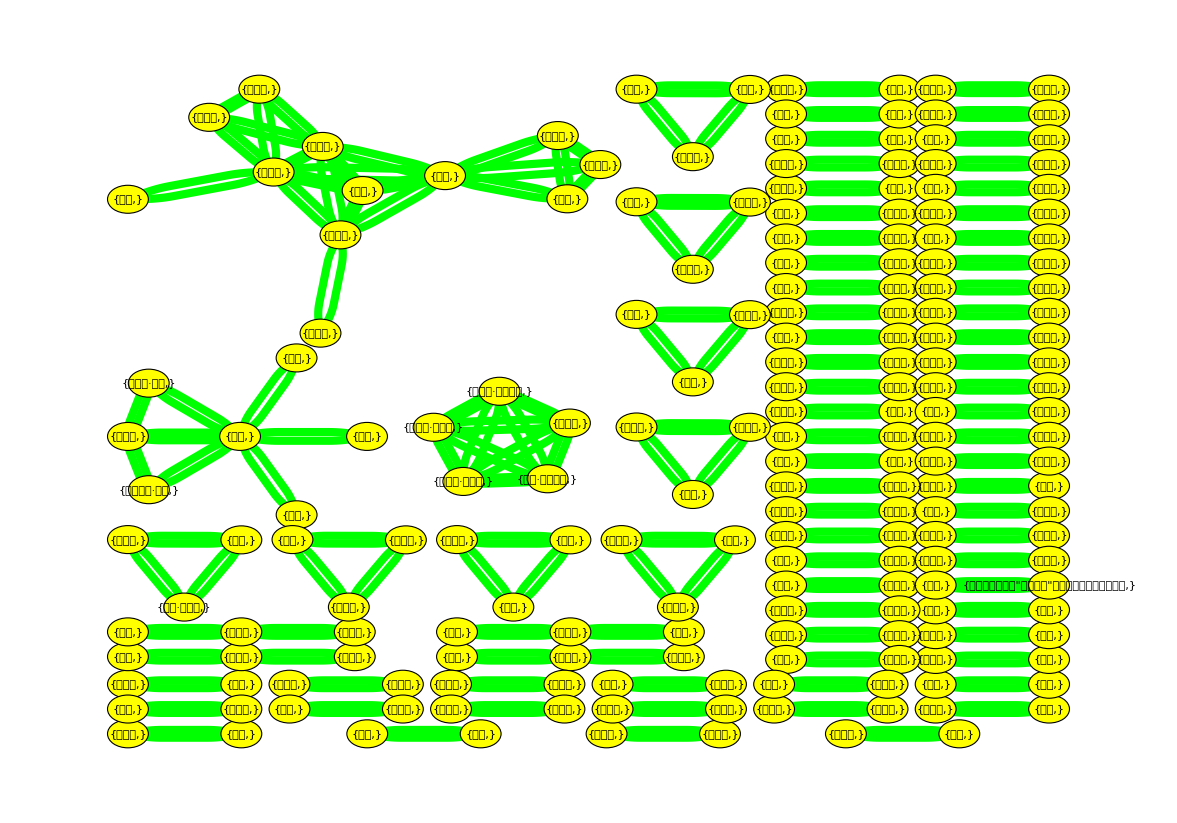

```mathematica
GraphPlot[Flatten[Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y}],VertexLabeling->True,VertexRenderingFunction->({Yellow,EdgeForm[Black],Disk[#,0.18],Black,Text[#2,#1]}&),PlotStyle->{Green,Arrowheads[{{0.1,0.8}}],Thickness[0.005]},AspectRatio->0.7,PlotRangePadding->1]
```

```mathematica
GraphPlot[single]
```

GraphPlot[{{{周勇,}},{{尹兴,}},{{张放,}},{{杨颖,}},{{陆亨,}},{{付玉辉,}},{{刘泱育,}},{{刘立华,}},{{史志高,}},{{周卷施,}},{{方建移,}},{{李承华,}},{{李玉洁,}},{{王晓兰,}},{{翁昌寿,}},{{肖叶飞,}},{{袁靖华,}},{{许子豪,}},{{郑从金,}},{{陈世华,}},{{陈力丹,}},{{陈建群,}},{{陈立新,}},{{本刊编辑部,}},{{《中国传媒发展指数报告》项目组,}},{{《中国媒介传播"维德守法"状况及评价报告》课题组,}},{{吴飞,},{丁志远,}},{{张健,},{佘贻明,}},{{罗斌,},{宋素红,}},{{张建中,},{任孟山,}},{{曾庆香,},{郭磊,}},{{陈力丹,},{王晶,}}}]

```mathematica
ScatterPlot
```

```mathematica
GraphPlot[Flatten[data,1]/.{x_,y_}:>{x->y}]
```

GraphPlot::grph: {{{ is not a valid graph.

GraphPlot[{{{于丹,},{张洪忠,},{杨东菊,}},{{于丹,},{杨东菊,},{张洪忠,}},{{张洪忠,},{于丹,},{杨东菊,}},{{张洪忠,},{杨东菊,},{于丹,}},{{杨东菊,},{于丹,},{张洪忠,}},{{杨东菊,},{张洪忠,},{于丹,}},{{张歆,},{郑笑眉,},{张琛,}},{{张歆,},{张琛,},{郑笑眉,}},{{郑笑眉,},{张歆,},{张琛,}},{{郑笑眉,},{张琛,},{张歆,}},{{张琛,},{张歆,},{郑笑眉,}},{{张琛,},{郑笑眉,},{张歆,}},{{薛可,},{陈晞,},{余明阳,}},{{薛可,},{余明阳,},{陈晞,}},{{陈晞,},{薛可,},{余明阳,}},{{陈晞,},{余明阳,},{薛可,}},{{余明阳,},{薛可,},{陈晞,}},{{余明阳,},{陈晞,},{薛可,}},{{刘寅斌,},{肖萍,},{陈永,}},{{刘寅斌,},{陈永,},{肖萍,}},{{肖萍,},{刘寅斌,},{陈永,}},{{肖萍,},{陈永,},{刘寅斌,}},{{陈永,},{刘寅斌,},{肖萍,}},{{陈永,},{肖萍,},{刘寅斌,}},{{刘自雄,},{许雯,},{高亚男,}},{{刘自雄,},{高亚男,},{许雯,}},{{许雯,},{刘自雄,},{高亚男,}},{{许雯,},{高亚男,},{刘自雄,}},{{高亚男,},{刘自雄,},{许雯,}},{{高亚男,},{许雯,},{刘自雄,}},{{张巨岩,},{巩昕崸,},{宋婧,}},{{张巨岩,},{宋婧,},{巩昕崸,}},{{巩昕崸,},{张巨岩,},{宋婧,}},{{巩昕崸,},{宋婧,},{张巨岩,}},{{宋婧,},{张巨岩,},{巩昕崸,}},{{宋婧,},{巩昕崸,},{张巨岩,}},{{翁昌寿,},{李建霞,},{方莉,}},{{翁昌寿,},{方莉,},{李建霞,}},{{李建霞,},{翁昌寿,},{方莉,}},{{李建霞,},{方莉,},{翁昌寿,}},{{方莉,},{翁昌寿,},{李建霞,}},{{方莉,},{李建霞,},{翁昌寿,}},{{尼古拉斯·卡尔,},{钟新,},{陆佳怡,}},{{尼古拉斯·卡尔,},{陆佳怡,},{钟新,}},{{钟新,},{尼古拉斯·卡尔,},{陆佳怡,}},{{钟新,},{陆佳怡,},{尼古拉斯·卡尔,}},{{陆佳怡,},{尼古拉斯·卡尔,},{钟新,}},{{陆佳怡,},{钟新,},{尼古拉斯·卡尔,}},{{菲利普·赛博,},{陆佳怡,},{钟新,}},{{菲利普·赛博,},{钟新,},{陆佳怡,}},{{陆佳怡,},{菲利普·赛博,},{钟新,}},{{陆佳怡,},{钟新,},{菲利普·赛博,}},{{钟新,},{菲利普·赛博,},{陆佳怡,}},{{钟新,},{陆佳怡,},{菲利普·赛博,}},{{马克·迪耶兹,},{周俊,},{李玉洁,}},{{马克·迪耶兹,},{李玉洁,},{周俊,}},{{周俊,},{马克·迪耶兹,},{李玉洁,}},{{周俊,},{李玉洁,},{马克·迪耶兹,}},{{李玉洁,},{马克·迪耶兹,},{周俊,}},{{李玉洁,},{周俊,},{马克·迪耶兹,}},{{赵晋,},{李彪,},{章含泽,}},{{赵晋,},{李彪,},{张盖伦,}},{{赵晋,},{章含泽,},{李彪,}},{{赵晋,},{章含泽,},{张盖伦,}},{{赵晋,},{张盖伦,},{李彪,}},{{赵晋,},{张盖伦,},{章含泽,}},{{李彪,},{赵晋,},{章含泽,}},{{李彪,},{赵晋,},{张盖伦,}},{{李彪,},{章含泽,},{赵晋,}},{{李彪,},{章含泽,},{张盖伦,}},{{李彪,},{张盖伦,},{赵晋,}},{{李彪,},{张盖伦,},{章含泽,}},{{章含泽,},{赵晋,},{李彪,}},{{章含泽,},{赵晋,},{张盖伦,}},{{章含泽,},{李彪,},{赵晋,}},{{章含泽,},{李彪,},{张盖伦,}},{{章含泽,},{张盖伦,},{赵晋,}},{{章含泽,},{张盖伦,},{李彪,}},{{张盖伦,},{赵晋,},{李彪,}},{{张盖伦,},{赵晋,},{章含泽,}},{{张盖伦,},{李彪,},{赵晋,}},{{张盖伦,},{李彪,},{章含泽,}},{{张盖伦,},{章含泽,},{赵晋,}},{{张盖伦,},{章含泽,},{李彪,}},{{喻国明,},{张佰明,},{胥琳佳,}},{{喻国明,},{张佰明,},{吴文汐,}},{{喻国明,},{胥琳佳,},{张佰明,}},{{喻国明,},{胥琳佳,},{吴文汐,}},{{喻国明,},{吴文汐,},{张佰明,}},{{喻国明,},{吴文汐,},{胥琳佳,}},{{张佰明,},{喻国明,},{胥琳佳,}},{{张佰明,},{喻国明,},{吴文汐,}},{{张佰明,},{胥琳佳,},{喻国明,}},{{张佰明,},{胥琳佳,},{吴文汐,}},{{张佰明,},{吴文汐,},{喻国明,}},{{张佰明,},{吴文汐,},{胥琳佳,}},{{胥琳佳,},{喻国明,},{张佰明,}},{{胥琳佳,},{喻国明,},{吴文汐,}},{{胥琳佳,},{张佰明,},{喻国明,}},{{胥琳佳,},{张佰明,},{吴文汐,}},{{胥琳佳,},{吴文汐,},{喻国明,}},{{胥琳佳,},{吴文汐,},{张佰明,}},{{吴文汐,},{喻国明,},{张佰明,}},{{吴文汐,},{喻国明,},{胥琳佳,}},{{吴文汐,},{张佰明,},{喻国明,}},{{吴文汐,},{张佰明,},{胥琳佳,}},{{吴文汐,},{胥琳佳,},{喻国明,}},{{吴文汐,},{胥琳佳,},{张佰明,}},{{喻国明,},{李彪,},{丁汉青,}},{{喻国明,},{李彪,},{王菲,}},{{喻国明,},{李彪,},{胥琳佳,}},{{喻国明,},{丁汉青,},{李彪,}},{{喻国明,},{丁汉青,},{王菲,}},{{喻国明,},{丁汉青,},{胥琳佳,}},{{喻国明,},{王菲,},{李彪,}},{{喻国明,},{王菲,},{丁汉青,}},{{喻国明,},{王菲,},{胥琳佳,}},{{喻国明,},{胥琳佳,},{李彪,}},{{喻国明,},{胥琳佳,},{丁汉青,}},{{喻国明,},{胥琳佳,},{王菲,}},{{李彪,},{喻国明,},{丁汉青,}},{{李彪,},{喻国明,},{王菲,}},{{李彪,},{喻国明,},{胥琳佳,}},{{李彪,},{丁汉青,},{喻国明,}},{{李彪,},{丁汉青,},{王菲,}},{{李彪,},{丁汉青,},{胥琳佳,}},{{李彪,},{王菲,},{喻国明,}},{{李彪,},{王菲,},{丁汉青,}},{{李彪,},{王菲,},{胥琳佳,}},{{李彪,},{胥琳佳,},{喻国明,}},{{李彪,},{胥琳佳,},{丁汉青,}},{{李彪,},{胥琳佳,},{王菲,}},{{丁汉青,},{喻国明,},{李彪,}},{{丁汉青,},{喻国明,},{王菲,}},{{丁汉青,},{喻国明,},{胥琳佳,}},{{丁汉青,},{李彪,},{喻国明,}},{{丁汉青,},{李彪,},{王菲,}},{{丁汉青,},{李彪,},{胥琳佳,}},{{丁汉青,},{王菲,},{喻国明,}},{{丁汉青,},{王菲,},{李彪,}},{{丁汉青,},{王菲,},{胥琳佳,}},{{丁汉青,},{胥琳佳,},{喻国明,}},{{丁汉青,},{胥琳佳,},{李彪,}},{{丁汉青,},{胥琳佳,},{王菲,}},{{王菲,},{喻国明,},{李彪,}},{{王菲,},{喻国明,},{丁汉青,}},{{王菲,},{喻国明,},{胥琳佳,}},{{王菲,},{李彪,},{喻国明,}},{{王菲,},{李彪,},{丁汉青,}},{{王菲,},{李彪,},{胥琳佳,}},{{王菲,},{丁汉青,},{喻国明,}},{{王菲,},{丁汉青,},{李彪,}},{{王菲,},{丁汉青,},{胥琳佳,}},{{王菲,},{胥琳佳,},{喻国明,}},{{王菲,},{胥琳佳,},{李彪,}},{{王菲,},{胥琳佳,},{丁汉青,}},{{胥琳佳,},{喻国明,},{李彪,}},{{胥琳佳,},{喻国明,},{丁汉青,}},{{胥琳佳,},{喻国明,},{王菲,}},{{胥琳佳,},{李彪,},{喻国明,}},{{胥琳佳,},{李彪,},{丁汉青,}},{{胥琳佳,},{李彪,},{王菲,}},{{胥琳佳,},{丁汉青,},{喻国明,}},{{胥琳佳,},{丁汉青,},{李彪,}},{{胥琳佳,},{丁汉青,},{王菲,}},{{胥琳佳,},{王菲,},{喻国明,}},{{胥琳佳,},{王菲,},{李彪,}},{{胥琳佳,},{王菲,},{丁汉青,}},{{乔治·索瓦凯斯,},{科斯塔·阿高什,},{阿西娜·佐托斯,}},{{乔治·索瓦凯斯,},{科斯塔·阿高什,},{安德烈·威格利斯,}},{{乔治·索瓦凯斯,},{科斯塔·阿高什,},{赵彦华,}},{{乔治·索瓦凯斯,},{阿西娜·佐托斯,},{科斯塔·阿高什,}},{{乔治·索瓦凯斯,},{阿西娜·佐托斯,},{安德烈·威格利斯,}},{{乔治·索瓦凯斯,},{阿西娜·佐托斯,},{赵彦华,}},{{乔治·索瓦凯斯,},{安德烈·威格利斯,},{科斯塔·阿高什,}},{{乔治·索瓦凯斯,},{安德烈·威格利斯,},{阿西娜·佐托斯,}},{{乔治·索瓦凯斯,},{安德烈·威格利斯,},{赵彦华,}},{{乔治·索瓦凯斯,},{赵彦华,},{科斯塔·阿高什,}},{{乔治·索瓦凯斯,},{赵彦华,},{阿西娜·佐托斯,}},{{乔治·索瓦凯斯,},{赵彦华,},{安德烈·威格利斯,}},{{科斯塔·阿高什,},{乔治·索瓦凯斯,},{阿西娜·佐托斯,}},{{科斯塔·阿高什,},{乔治·索瓦凯斯,},{安德烈·威格利斯,}},{{科斯塔·阿高什,},{乔治·索瓦凯斯,},{赵彦华,}},{{科斯塔·阿高什,},{阿西娜·佐托斯,},{乔治·索瓦凯斯,}},{{科斯塔·阿高什,},{阿西娜·佐托斯,},{安德烈·威格利斯,}},{{科斯塔·阿高什,},{阿西娜·佐托斯,},{赵彦华,}},{{科斯塔·阿高什,},{安德烈·威格利斯,},{乔治·索瓦凯斯,}},{{科斯塔·阿高什,},{安德烈·威格利斯,},{阿西娜·佐托斯,}},{{科斯塔·阿高什,},{安德烈·威格利斯,},{赵彦华,}},{{科斯塔·阿高什,},{赵彦华,},{乔治·索瓦凯斯,}},{{科斯塔·阿高什,},{赵彦华,},{阿西娜·佐托斯,}},{{科斯塔·阿高什,},{赵彦华,},{安德烈·威格利斯,}},{{阿西娜·佐托斯,},{乔治·索瓦凯斯,},{科斯塔·阿高什,}},{{阿西娜·佐托斯,},{乔治·索瓦凯斯,},{安德烈·威格利斯,}},{{阿西娜·佐托斯,},{乔治·索瓦凯斯,},{赵彦华,}},{{阿西娜·佐托斯,},{科斯塔·阿高什,},{乔治·索瓦凯斯,}},{{阿西娜·佐托斯,},{科斯塔·阿高什,},{安德烈·威格利斯,}},{{阿西娜·佐托斯,},{科斯塔·阿高什,},{赵彦华,}},{{阿西娜·佐托斯,},{安德烈·威格利斯,},{乔治·索瓦凯斯,}},{{阿西娜·佐托斯,},{安德烈·威格利斯,},{科斯塔·阿高什,}},{{阿西娜·佐托斯,},{安德烈·威格利斯,},{赵彦华,}},{{阿西娜·佐托斯,},{赵彦华,},{乔治·索瓦凯斯,}},{{阿西娜·佐托斯,},{赵彦华,},{科斯塔·阿高什,}},{{阿西娜·佐托斯,},{赵彦华,},{安德烈·威格利斯,}},{{安德烈·威格利斯,},{乔治·索瓦凯斯,},{科斯塔·阿高什,}},{{安德烈·威格利斯,},{乔治·索瓦凯斯,},{阿西娜·佐托斯,}},{{安德烈·威格利斯,},{乔治·索瓦凯斯,},{赵彦华,}},{{安德烈·威格利斯,},{科斯塔·阿高什,},{乔治·索瓦凯斯,}},{{安德烈·威格利斯,},{科斯塔·阿高什,},{阿西娜·佐托斯,}},{{安德烈·威格利斯,},{科斯塔·阿高什,},{赵彦华,}},{{安德烈·威格利斯,},{阿西娜·佐托斯,},{乔治·索瓦凯斯,}},{{安德烈·威格利斯,},{阿西娜·佐托斯,},{科斯塔·阿高什,}},{{安德烈·威格利斯,},{阿西娜·佐托斯,},{赵彦华,}},{{安德烈·威格利斯,},{赵彦华,},{乔治·索瓦凯斯,}},{{安德烈·威格利斯,},{赵彦华,},{科斯塔·阿高什,}},{{安德烈·威格利斯,},{赵彦华,},{阿西娜·佐托斯,}},{{赵彦华,},{乔治·索瓦凯斯,},{科斯塔·阿高什,}},{{赵彦华,},{乔治·索瓦凯斯,},{阿西娜·佐托斯,}},{{赵彦华,},{乔治·索瓦凯斯,},{安德烈·威格利斯,}},{{赵彦华,},{科斯塔·阿高什,},{乔治·索瓦凯斯,}},{{赵彦华,},{科斯塔·阿高什,},{阿西娜·佐托斯,}},{{赵彦华,},{科斯塔·阿高什,},{安德烈·威格利斯,}},{{赵彦华,},{阿西娜·佐托斯,},{乔治·索瓦凯斯,}},{{赵彦华,},{阿西娜·佐托斯,},{科斯塔·阿高什,}},{{赵彦华,},{阿西娜·佐托斯,},{安德烈·威格利斯,}},{{赵彦华,},{安德烈·威格利斯,},{乔治·索瓦凯斯,}},{{赵彦华,},{安德烈·威格利斯,},{科斯塔·阿高什,}},{{赵彦华,},{安德烈·威格利斯,},{阿西娜·佐托斯,}}}]